```mathematica
thz2waavenum=1/0.0299792458;SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-70_phon_dos"];
phDOSfiles={"1.total_dos.dat","2.total_dos.dat","3.total_dos.dat","4.total_dos.dat","5.total_dos.dat","6.total_dos.dat","7.total_dos.dat","8.total_dos.dat","9.total_dos.dat","10.total_dos.dat","11.total_dos.dat"};
fren70dos=Table[ReadList[phDOSfiles[[i]],{Number,Number}],{i,1,Length@phDOSfiles}];
```

```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/cvac_phon_dos"];
cvac=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,9}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/perf_phon_dos"];
perf=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,9}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-1126_phon_dos"];
fren1126=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-129_phon_dos"];
fren129=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-142_phon_dos"];
fren142=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-174_phon_dos"];
fren174=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-70_phon_dos"];
fren70=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
```

```mathematica
names={"perf","fren129","fren142","fren70","fren174","fren1126","cvac"};
objects={perf,fren129,fren142,fren70,fren174,fren1126,cvac};
alatts={4.575,4.600,4.625,4.6583,4.685,4.730,4.759,4.801,4.850,4.875,4.900};
vols=(alatts*2)^3/64;
fren1126Data=Table[Table[Flatten[{(fren1126[[j]][[i]][[1]]*thz2waavenum),vols[[j]],fren1126[[j]][[i]][[2]]}],{i,1,Length@fren1126[[j]]}],{j,1,Length@vols}];
```

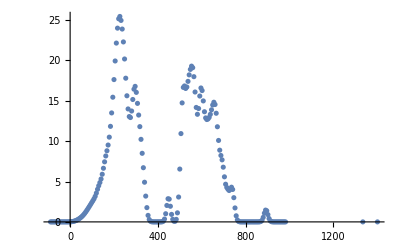

```mathematica
ListPlot@Transpose[{Transpose[fren1126Data[[1]]][[1]],Transpose[fren1126Data[[1]]][[3]]}]
```

```mathematica
fren1126Data2D=Table[Table[Flatten[{fren1126[[j]][[i]][[1]]*thz2waavenum,fren1126[[j]][[i]][[2]]+10*vols[[j]]}],{i,1,Length@fren1126[[j]]}],{j,1,Length@vols}];
data=Table[Table[Table[Flatten[{objects[[k]][[j]][[i]][[1]]*thz2waavenum,vols[[j]],objects[[k]][[j]][[i]][[2]]}],{i,1,Length@objects[[k]][[j]]}],{j,1,Length@objects[[k]]}],{k,1,Length@objects}];
data2D=Table[Table[Table[Flatten[{objects[[k]][[j]][[i]][[1]]*thz2waavenum,objects[[k]][[j]][[i]][[2]]}],{i,1,Length@objects[[k]][[j]]}],{j,1,Length@objects[[k]]}],{k,1,Length@objects}];
```

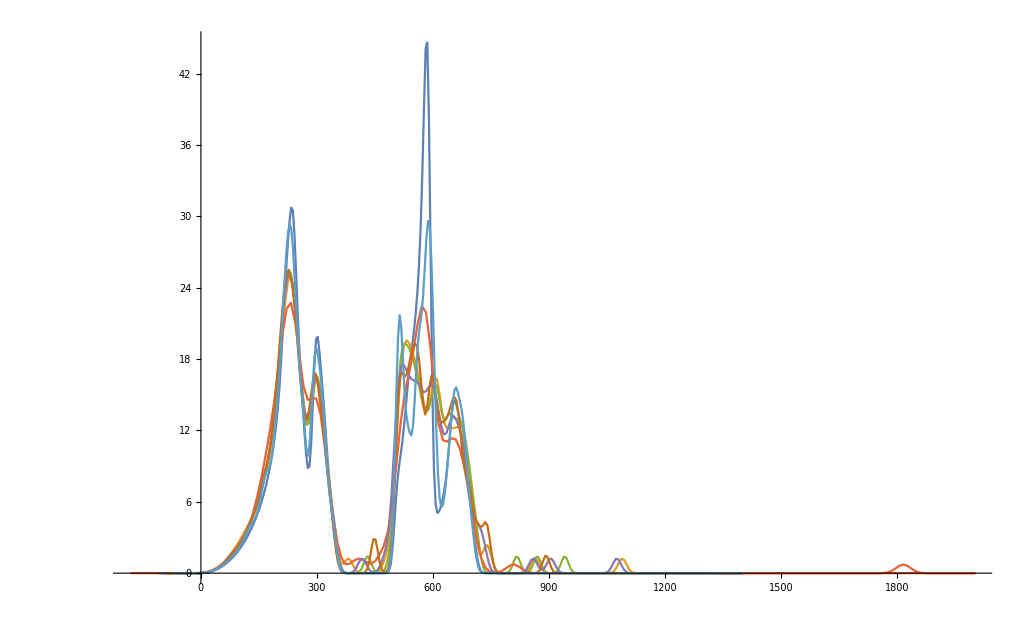

```mathematica
ListLinePlot@Table[data2D[[i]][[1]],{i,1,Length@data2D}]
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Raman/RESULTS_Raman/"];
expRaman=ReadList[{"DCmelt011.normalised"}[[1]],{Number,Number,Number}];
```

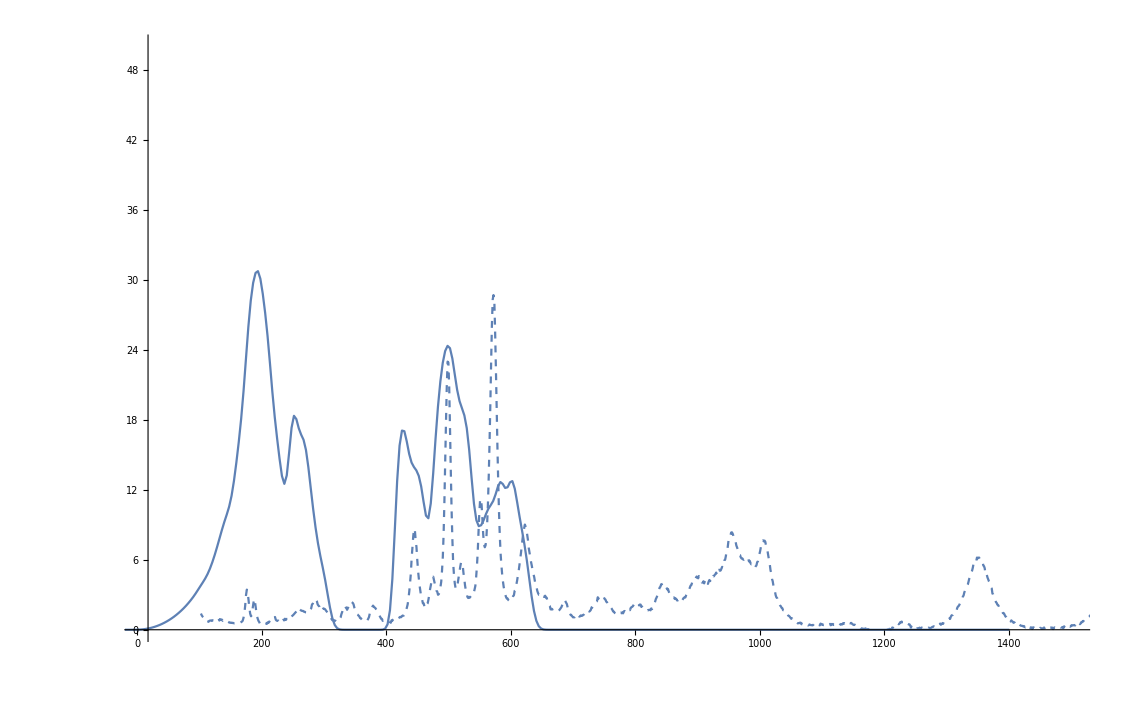

```mathematica
Show[{ListLinePlot[Table[data2D[[i]][[6]],{i,7,7}],PlotRange->{{10,1500},{0,50}}],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1500},{0,50}},PlotStyle->Dashed]}]
```

```mathematica
names
```

{perf,fren129,fren142,fren70,fren174,fren1126,cvac}

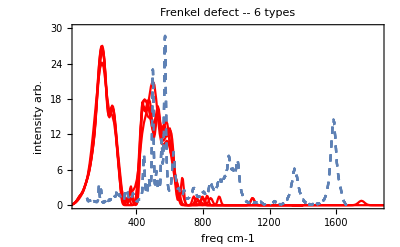

```mathematica
Table[With[{defect=i,vol=6},Show[{ListLinePlot[data2D[[defect]][[vol]],Frame->True,FrameLabel->{"freq cm-1","intensity arb."},PlotStyle->Red,PlotRange->{{50,1850},{0,30}},PlotLabel->"Frenkel defect -- 6 types"],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed]}]],{i,2,6,1}]//Show
```

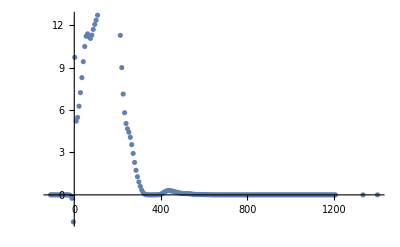

```mathematica
thzToKelvin=47.99243415908;
popBE[{waveNum_,Intensity_},temp_,scale_]:={waveNum,scale*Intensity/(Exp[waveNum*(thzToKelvin/thz2waavenum)/temp]-1)}
ListPlot@Table[popBE[data2D[[2]][[6]][[i]],100,10],{i,1,Length@data2D[[2]][[6]]}]
```

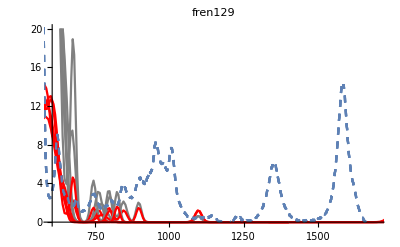

```mathematica
Table[With[{defect=i,vol=6},Show[{ListLinePlot[Table[popBE[data2D[[defect]][[vol]][[i]],300,100],{i,1,203}],PlotRange->{{600,1700},{0,20}},PlotStyle->Gray,PlotLabel->names[[defect]]],ListLinePlot[data2D[[defect]][[vol]],PlotStyle->Red],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed]}]],{i,2,6,1}]//Show
```

```mathematica
names2={"Perfet Zr32C32","Frenkel Zr32C32 -- Bound Dimer","Frenkel Zr32C32 -- Bound Trimer","Frenkel Zr32C32 -- Unbound Dimer","Frenkel Zr32C32 -- Unbound Trimer","Frenkel Zr32C32 -- Unbound Tetramer","CVAC Zr32C31 - 3 C at. %"};
```

#### Perfect DOS and Raman

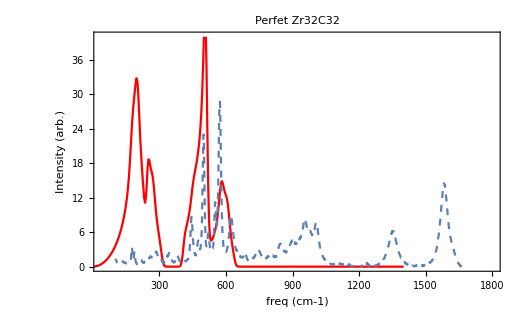

```mathematica
With[{defect=1,vol=6},Show[{ListLinePlot[data2D[[defect]][[vol]],PlotRange->{{40,1800},{0,40}},Frame->True,FrameLabel->{"freq (cm-1)","Intensity (arb.)"},PlotLegends->Placed[{"DFT"},{0.7,0.7}],PlotStyle->Red,PlotLabel->names2[[defect]]],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed,PlotLegends->Placed[{"Exp"},{0.7,0.7}]]}]]
```

#### Perfect DOS convolution

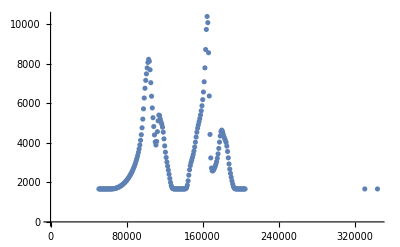

```mathematica
ListPlot@Sum[Table[data2D[[1]][[6]][[j]]+data2D[[1]][[6]][[i]],{i,1,203}],{j,1,200}]
```

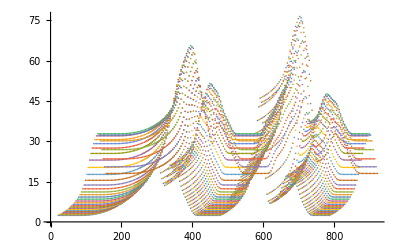

```mathematica
ListPlot@Table[Table[{Transpose[data2D[[1]][[6]]][[1]][[i]]+Transpose[data2D[[1]][[6]]][[1]][[j]],Transpose[data2D[[1]][[6]]][[2]][[i]]+Transpose[data2D[[1]][[6]]][[2]][[j]]},{i,1,200}],{j,40,75}]
```

```mathematica
jFun[x_,arg_]:=If[x<arg[[1]][[1]],0,Evaluate[If[x>arg[[-1]][[1]],0,Interpolation[arg][x]]]]
```

```mathematica
test=Table[jFun[x,Table[Table[{Transpose[data2D[[1]][[6]]][[1]][[i]]+Transpose[data2D[[1]][[6]]][[1]][[j]],Transpose[data2D[[1]][[6]]][[2]][[i]]+Transpose[data2D[[1]][[6]]][[2]][[j]]},{i,1,200}],{j,1,200}][[k]]],{k,1,200}];
```

```mathematica
sum=(1/200)Sum[test[[i]],{i,0,200}]
```

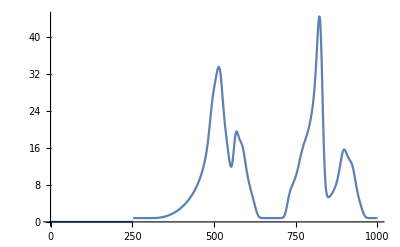

```mathematica
Plot[test[[100]],{x,0,1000}]
```

```mathematica
Plot[test[[1]],{x,0,1400}]
```

$Aborted

```mathematica
jdos=Table[Table[{Transpose[data2D[[1]][[6]]][[1]][[i]]+Transpose[data2D[[1]][[6]]][[1]][[j]],Transpose[data2D[[1]][[6]]][[2]][[i]]+Transpose[data2D[[1]][[6]]][[2]][[j]]},{i,1,200}],{j,1,200}];
```

```mathematica
jdosSmall=Table[Table[{Transpose[data2D[[1]][[6]]][[1]][[i]]+Transpose[data2D[[1]][[6]]][[1]][[j]],Transpose[data2D[[1]][[6]]][[2]][[i]]+Transpose[data2D[[1]][[6]]][[2]][[j]]},{i,1,200}],{j,1,200}];
```

```mathematica
Transpose[data2D[[1]][[6]]][[2]][[1;;40]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,5.×10^-10,1.05×10^-8,1.434×10^-7,1.4078×10^-6,0.0000101887,0.0000565086,0.000251538,0.000932411,0.00291756,0.00769873,0.0172062,0.0331655,0.0566647,0.0882733,0.128332,0.177083,0.234767,0.301681,0.378112,0.464385,0.560871,0.667922,0.785934,0.915332,1.05653,1.20999,1.37622,1.55573,1.74913,1.95704,2.18021,2.41947}

```mathematica
Transpose[data2D[[1]][[6]]][[1]][[1;;40]]
```

{-64.0056,-60.1615,-56.3175,-52.4734,-48.6294,-44.7853,-40.9412,-37.0972,-33.2531,-29.4091,-25.565,-21.721,-17.8769,-14.0328,-10.1888,-6.34473,-2.50068,1.34338,5.18744,9.03149,12.8756,16.7196,20.5637,24.4077,28.2518,32.0958,35.9399,39.7839,43.628,47.4721,51.3161,55.1602,59.0042,62.8483,66.6923,70.5364,74.3805,78.2245,82.0686,85.9126}

```mathematica
jdosSmall//Dimensions
```

{200,200,2}

```mathematica
jdosSmall[[20]][[1]]
```

{-54.9741,0.0331655}

```mathematica
jdosSmall[[100]][[1]][[1]]
```

252.55

```mathematica
Min[Transpose[jdosSmall[[100]]][[1]]]
Max[Transpose[jdosSmall[[100]]][[1]]]
```

252.55

1017.52

```mathematica
jdosSmall[[1]][[1]][[1]]
```

-128.011

```mathematica
jFun[x,jdosSmall[[1]]];
```

```mathematica
jdosSmall[[50]]
```

{{60.3476,6.00718},{64.1917,6.00718},{68.0357,6.00718},{71.8798,6.00718},{75.7238,6.00718},{79.5679,6.00718},{83.4119,6.00718},{87.256,6.00718},{91.1001,6.00718},{94.9441,6.00718},{98.7882,6.00718},{102.632,6.00718},{106.476,6.00718},{110.32,6.00718},{114.164,6.00718},{118.008,6.00718},{121.853,6.00718},{125.697,6.00719},{129.541,6.0072},{133.385,6.00721},{137.229,6.00723},{141.073,6.00726},{144.917,6.00729},{148.761,6.00733},{152.605,6.00737},{156.449,6.00741},{160.293,6.00746},{164.137,6.00751},{167.981,6.00757},{171.825,6.00762},{175.669,6.00769},{179.513,6.00775},{183.357,6.00782},{187.201,6.00789},{191.046,6.00797},{194.89,6.00804},{198.734,6.00812},{202.578,6.00821},{206.422,6.0083},{210.266,6.00839},{214.11,6.00848},{217.954,6.00858},{221.798,6.00869},{225.642,6.0088},{229.486,6.00891},{233.33,6.00903},{237.174,6.00916},{241.018,6.00929},{244.862,6.00943},{248.706,6.00958},{252.55,6.00974},{256.394,6.00992},{260.239,6.01011},{264.083,6.01031},{267.927,6.01054},{271.771,6.01079},{275.615,6.01108},{279.459,6.01142},{283.303,6.01183},{287.147,6.01233},{290.991,6.01297},{294.835,6.01371},{298.679,6.01448},{302.523,6.01513},{306.367,6.01562},{310.211,6.01599},{314.055,6.01631},{317.899,6.01658},{321.743,6.01668},{325.588,6.0164},{329.432,6.01566},{333.276,6.01464},{337.12,6.0136},{340.964,6.01271},{344.808,6.01198},{348.652,6.01133},{352.496,6.01073},{356.34,6.01023},{360.184,6.00999},{364.028,6.01018},{367.872,6.01075},{371.716,6.01138},{375.56,6.01168},{379.404,6.01159},{383.248,6.01133},{387.092,6.01111},{390.936,6.01094},{394.781,6.01073},{398.625,6.0104},{402.469,6.00999},{406.313,6.00957},{410.157,6.0092},{414.001,6.00889},{417.845,6.00863},{421.689,6.00839},{425.533,6.00817},{429.377,6.00794},{433.221,6.00772},{437.065,6.00751},{440.909,6.00735},{444.753,6.00725},{448.597,6.0072},{452.441,6.00718},{456.285,6.00718},{460.129,6.00718},{463.974,6.00718},{467.818,6.00718},{471.662,6.00718},{475.506,6.00718},{479.35,6.00718},{483.194,6.00718},{487.038,6.00718},{490.882,6.00718},{494.726,6.00718},{498.57,6.00718},{502.414,6.00718},{506.258,6.00718},{510.102,6.00718},{513.946,6.00718},{517.79,6.00719},{521.634,6.00723},{525.478,6.00734},{529.323,6.00751},{533.167,6.00774},{537.011,6.00795},{540.855,6.00811},{544.699,6.00823},{548.543,6.00832},{552.387,6.00842},{556.231,6.00852},{560.075,6.00864},{563.919,6.00879},{567.763,6.00896},{571.607,6.00914},{575.451,6.0093},{579.295,6.00944},{583.139,6.00954},{586.983,6.00964},{590.827,6.00974},{594.671,6.00985},{598.516,6.00998},{602.36,6.01014},{606.204,6.01034},{610.048,6.01058},{613.892,6.01091},{617.736,6.01137},{621.58,6.01197},{625.424,6.01263},{629.268,6.01303},{633.112,6.01278},{636.956,6.01174},{640.8,6.01027},{644.644,6.00898},{648.488,6.0082},{652.332,6.00786},{656.176,6.00776},{660.02,6.00776},{663.864,6.00779},{667.709,6.00784},{671.553,6.00789},{675.397,6.00795},{679.241,6.00803},{683.085,6.00813},{686.929,6.00826},{690.773,6.00842},{694.617,6.00861},{698.461,6.00878},{702.305,6.0089},{706.149,6.00894},{709.993,6.00889},{713.837,6.0088},{717.681,6.00872},{721.525,6.00865},{725.369,6.00859},{729.213,6.00852},{733.058,6.00841},{736.902,6.00825},{740.746,6.00806},{744.59,6.00789},{748.434,6.00774},{752.278,6.00761},{756.122,6.0075},{759.966,6.0074},{763.81,6.00731},{767.654,6.00725},{771.498,6.00721},{775.342,6.00719},{779.186,6.00718},{783.03,6.00718},{786.874,6.00718},{790.718,6.00718},{794.562,6.00718},{798.406,6.00718},{802.251,6.00718},{806.095,6.00718},{809.939,6.00718},{813.783,6.00718},{817.627,6.00718},{821.471,6.00718},{825.315,6.00718}}

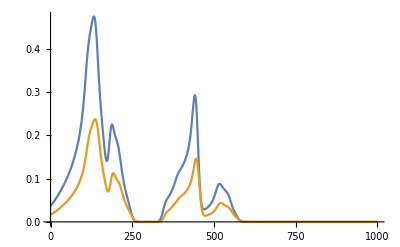

```mathematica
Plot[{jFun[x,jdosSmall[[1]]],jFun[x,jdosSmall[[2]]]},{x,0,1000},PlotRange->All]
```

```mathematica
dos=Interpolation[data2D[[1]][[6]]][x]
```

InterpolatingFunction[{{-64.0056, 1400.97}}, <>][x]

```mathematica
jdos//Length
```

200

```mathematica
actualJDOS=With[{n=200},(1/n)Sum[jFun[x,jdos[[i]]],{i,1,n}]];
```

```mathematica
1
```

```mathematica
Plot[Sum[jFun[x,jdosSmall[[i]]],{i,1,150}],{x,-100,550}]
```

```mathematica
actualJDOS=With[{n=200},(1/n)Sum[Interpolation[jdos[[i]]][x],{i,n}]]//Simplify;
```

InterpolatingFunction::dmval: Input value {-9.98345} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

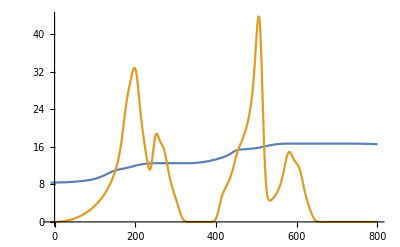

```mathematica
Plot[{actualJDOS,dos},{x,-10,800}]
```

```mathematica
jdos=Table[Table[{Transpose[data2D[[1]][[6]]][[1]][[i]]+Transpose[data2D[[1]][[6]]][[1]][[j]],Transpose[data2D[[1]][[6]]][[2]][[i]]+Transpose[data2D[[1]][[6]]][[2]][[j]]},{i,1,200}],{j,1,200}];
```

```mathematica
jFun[x,Transpose[data2D[[1]][[6]]][[2]]]
```

Part::partd: Part specification 0.⟦1⟧ is longer than depth of object.

If[x<0.⟦1⟧,0,If[x>{0.,0.,0.,0.,0.,0.,0.,0.,5.×10^-10,1.05×10^-8,1.434×10^-7,1.4078×10^-6,0.0000101887,0.0000565086,0.000251538,0.000932411,0.00291756,0.00769873,0.0172062,0.0331655,0.0566647,0.0882733,0.128332,0.177083,0.234767,0.301681,0.378112,0.464385,0.560871,0.667922,0.785934,0.915332,1.05653,1.20999,1.37622,1.55573,1.74913,1.95704,2.18021,2.41947,2.67576,2.95018,3.244,3.55869,3.89599,4.25792,4.64686,5.06567,5.51774,6.00718,6.53901,7.11944,7.75628,8.45957,9.24255,10.1234,11.1287,12.3004,13.7089,15.4605,17.6549,20.2562,22.9859,25.4499,27.447,29.0904,30.6003,31.9752,32.7724,32.27,30.125,26.8586,23.4389,20.4797,18.0076,15.7797,13.6623,11.888,11.1087,12.0075,14.4807,17.2235,18.6823,18.526,17.6552,16.9129,16.3624,15.607,14.3489,12.6637,10.8839,9.28894,7.95074,6.80561,5.76391,4.74982,3.70896,2.6392,1.63064,0.832831,0.336933,0.104448,0.0242147,0.00412626,0.000510505,0.0000454558,2.8944×10^-6,1.312×10^-7,4.2×10^-9,1.×10^-10,0.,0.,6.×10^-10,2.62×10^-8,7.557×10^-7,0.0000153897,0.000221919,0.00227459,0.0166584,0.0878281,0.337003,0.956447,2.05693,3.47329,4.83667,5.89631,6.67451,7.32708,7.98223,8.71275,9.57147,10.6051,11.8173,13.1151,14.3319,15.3514,16.1943,16.9709,17.7855,18.7036,19.7698,21.0334,22.5704,24.5124,27.0876,30.6125,35.2476,40.318,43.6051,42.0375,34.4346,23.5,13.7817,7.84041,5.28109,4.56999,4.58524,4.84777,5.21845,5.67332,6.22356,6.9008,7.75903,8.86472,10.2513,11.8418,13.3864,14.4985,14.8718,14.5442,13.8727,13.2188,12.7217,12.3034,11.7504,10.8284,9.46745,7.86357,6.32354,5.0203,3.93471,2.9676,2.06025,1.24848,0.626871,0.24955,0.0761402,0.0173734,0.00291345,0.000354685,0.0000310723,1.9464×10^-6,8.68×10^-8,2.7×10^-9,1.×10^-10,0.,0.,0.,0.,0.,0.,0.,0.}⟦1⟧⟦-1⟧,0,Interpolation[{0.,0.,0.,0.,0.,0.,0.,0.,5.×10^-10,1.05×10^-8,1.434×10^-7,1.4078×10^-6,0.0000101887,0.0000565086,0.000251538,0.000932411,0.00291756,0.00769873,0.0172062,0.0331655,0.0566647,0.0882733,0.128332,0.177083,0.234767,0.301681,0.378112,0.464385,0.560871,0.667922,0.785934,0.915332,1.05653,1.20999,1.37622,1.55573,1.74913,1.95704,2.18021,2.41947,2.67576,2.95018,3.244,3.55869,3.89599,4.25792,4.64686,5.06567,5.51774,6.00718,6.53901,7.11944,7.75628,8.45957,9.24255,10.1234,11.1287,12.3004,13.7089,15.4605,17.6549,20.2562,22.9859,25.4499,27.447,29.0904,30.6003,31.9752,32.7724,32.27,30.125,26.8586,23.4389,20.4797,18.0076,15.7797,13.6623,11.888,11.1087,12.0075,14.4807,17.2235,18.6823,18.526,17.6552,16.9129,16.3624,15.607,14.3489,12.6637,10.8839,9.28894,7.95074,6.80561,5.76391,4.74982,3.70896,2.6392,1.63064,0.832831,0.336933,0.104448,0.0242147,0.00412626,0.000510505,0.0000454558,2.8944×10^-6,1.312×10^-7,4.2×10^-9,1.×10^-10,0.,0.,6.×10^-10,2.62×10^-8,7.557×10^-7,0.0000153897,0.000221919,0.00227459,0.0166584,0.0878281,0.337003,0.956447,2.05693,3.47329,4.83667,5.89631,6.67451,7.32708,7.98223,8.71275,9.57147,10.6051,11.8173,13.1151,14.3319,15.3514,16.1943,16.9709,17.7855,18.7036,19.7698,21.0334,22.5704,24.5124,27.0876,30.6125,35.2476,40.318,43.6051,42.0375,34.4346,23.5,13.7817,7.84041,5.28109,4.56999,4.58524,4.84777,5.21845,5.67332,6.22356,6.9008,7.75903,8.86472,10.2513,11.8418,13.3864,14.4985,14.8718,14.5442,13.8727,13.2188,12.7217,12.3034,11.7504,10.8284,9.46745,7.86357,6.32354,5.0203,3.93471,2.9676,2.06025,1.24848,0.626871,0.24955,0.0761402,0.0173734,0.00291345,0.000354685,0.0000310723,1.9464×10^-6,8.68×10^-8,2.7×10^-9,1.×10^-10,0.,0.,0.,0.,0.,0.,0.,0.}][x]]]

```mathematica
Transpose[data2D[[1]][[6]]][[1]][[200]]
```

700.962

```mathematica
ListConvolve[data2D[[1]][[6]],data2D[[1]][[6]]]
```

{{967624.}}

#### CVAC DOS and Raman

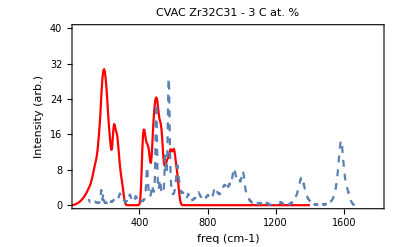

```mathematica
With[{defect=7,vol=6},Show[{ListLinePlot[data2D[[defect]][[vol]],PlotRange->{{40,1800},{0,40}},Frame->True,FrameLabel->{"freq (cm-1)","Intensity (arb.)"},PlotLegends->Placed[{"DFT"},{0.7,0.7}],PlotStyle->Red,PlotLabel->names2[[defect]]],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed,PlotLegends->Placed[{"Exp"},{0.7,0.7}]]}]]
```

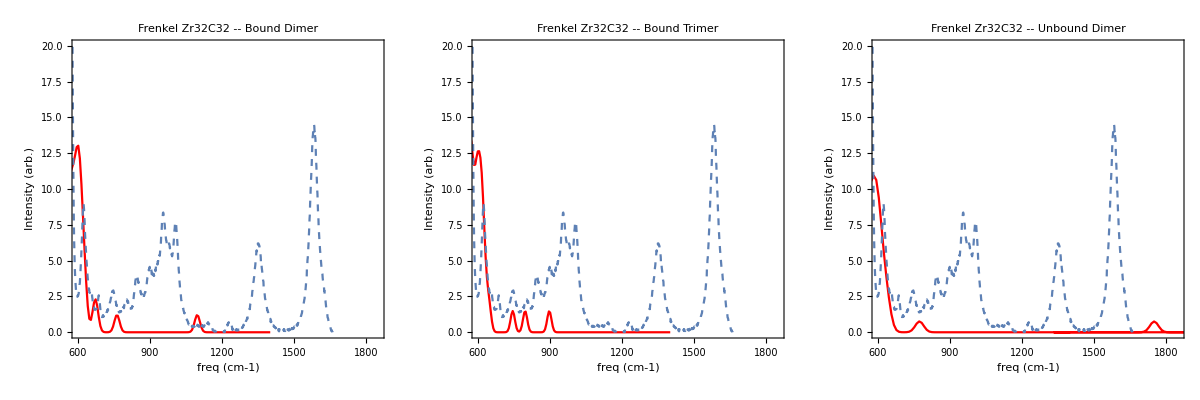

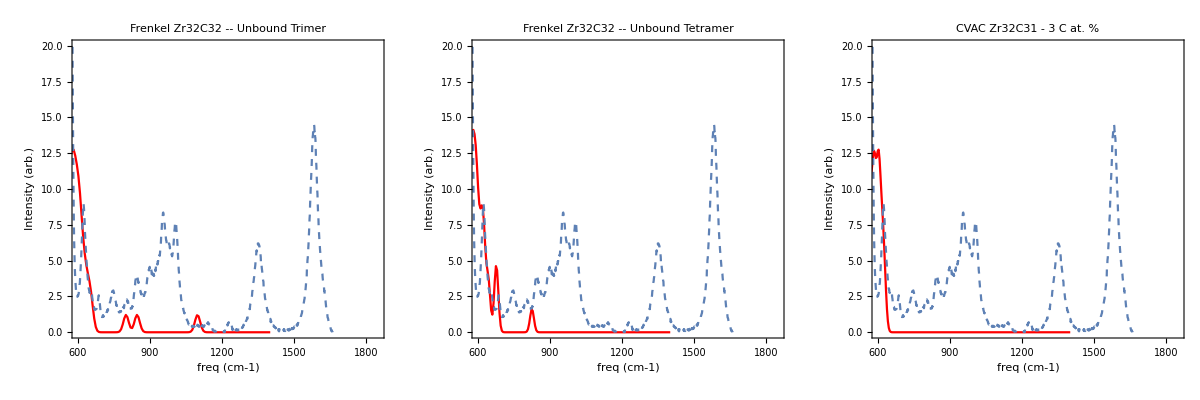

```mathematica
GraphicsGrid[{Table[With[{defect=i,vol=6},Show[{ListLinePlot[data2D[[defect]][[vol]],PlotRange->{{600,1850},{0,20}},Frame->True,FrameLabel->{"freq (cm-1)","Intensity (arb.)"},PlotLegends->Placed[{"DFT"},{0.5,0.7}],PlotStyle->Red,PlotLabel->names2[[defect]]],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed,PlotLegends->Placed[{"Exp"},{0.5,0.7}]]}]],{i,2,4,1}]},ImageSize->1200,Spacings->0]
GraphicsGrid[{Table[With[{defect=i,vol=6},Show[{ListLinePlot[data2D[[defect]][[vol]],PlotRange->{{600,1850},{0,20}},Frame->True,FrameLabel->{"freq (cm-1)","Intensity (arb.)"},PlotLegends->Placed[{"DFT"},{0.5,0.7}],PlotStyle->Red,PlotLabel->names2[[defect]]],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotLegends->Placed[{"Exp"},{0.5,0.7}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed]}]],{i,5,7,1}]},ImageSize->1200,Spacings->0]
```

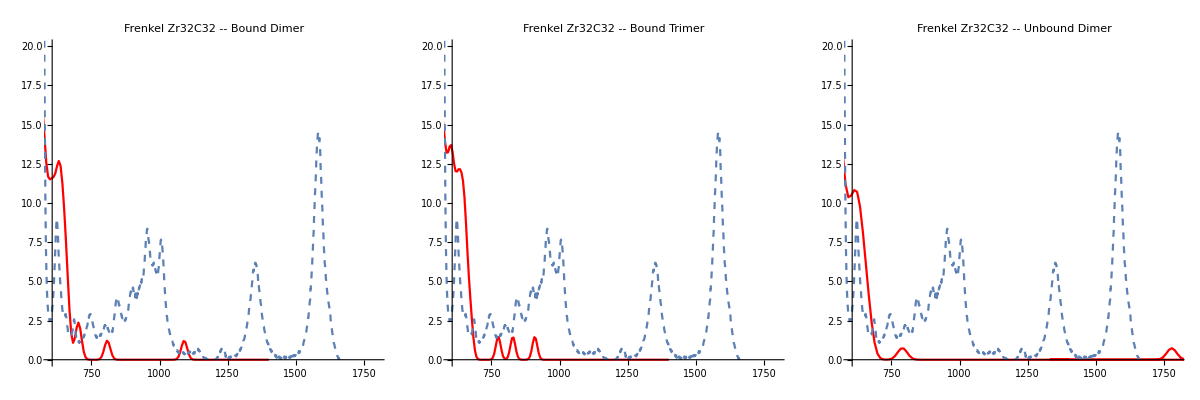

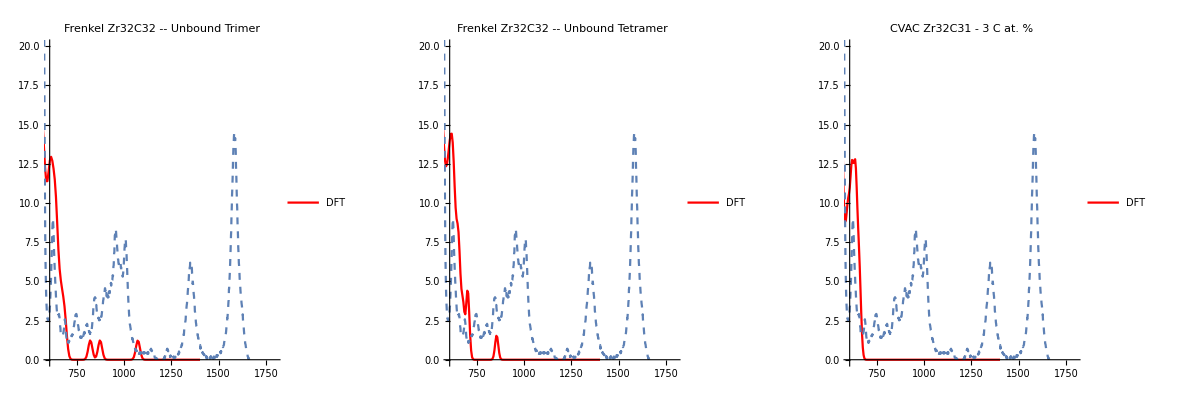

-Graphics-

```mathematica
GraphicsGrid[{Table[With[{defect=i,vol=4},Show[{ListLinePlot[data2D[[defect]][[vol]],PlotRange->{{600,1800},{0,20}},PlotLegends->Placed[{"DFT"},{0.7,0.7}],PlotStyle->Red,PlotLabel->names2[[defect]]],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed,PlotLegends->Placed[{"Exp"},{0.7,0.7}]]}]],{i,2,4,1}]},ImageSize->1200,Spacings->0]
GraphicsGrid[{Table[With[{defect=i,vol=4},Show[{ListLinePlot[data2D[[defect]][[vol]],PlotRange->{{600,1800},{0,20}},PlotLegends->Placed[{"DFT"},{0.7,0.7}],PlotStyle->Red,PlotLabel->names2[[defect]]],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed]}]],{i,5,7,1}]},ImageSize->1200,Spacings->0]
```

Gap states

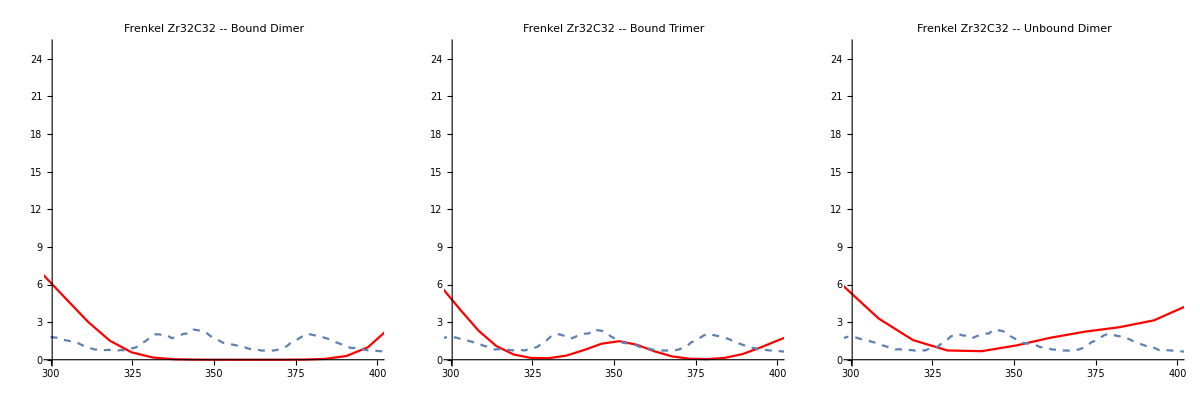

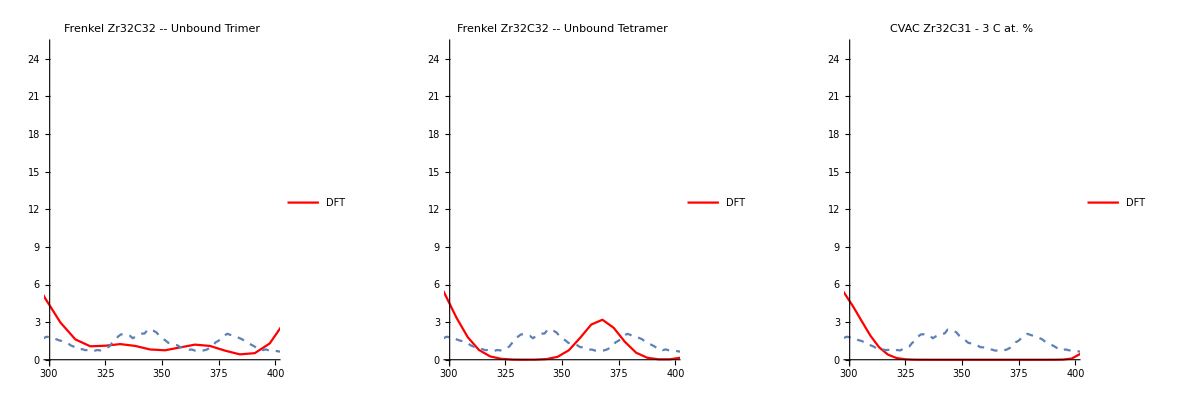

```mathematica
Gap states
GraphicsGrid[{Table[With[{defect=i,vol=6},Show[{ListLinePlot[data2D[[defect]][[vol]],PlotRange->{{300,400},{0,25}},PlotLegends->Placed[{"DFT"},{0.7,0.7}],PlotStyle->Red,PlotLabel->names2[[defect]]],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed,PlotLegends->Placed[{"Exp"},{0.7,0.7}]]}]],{i,2,4,1}]},ImageSize->1200,Spacings->0]
GraphicsGrid[{Table[With[{defect=i,vol=6},Show[{ListLinePlot[data2D[[defect]][[vol]],PlotRange->{{300,400},{0,25}},PlotLegends->Placed[{"DFT"},{0.7,0.7}],PlotStyle->Red,PlotLabel->names2[[defect]]],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed]}]],{i,5,7,1}]},ImageSize->1200,Spacings->0]
```

Carbon states

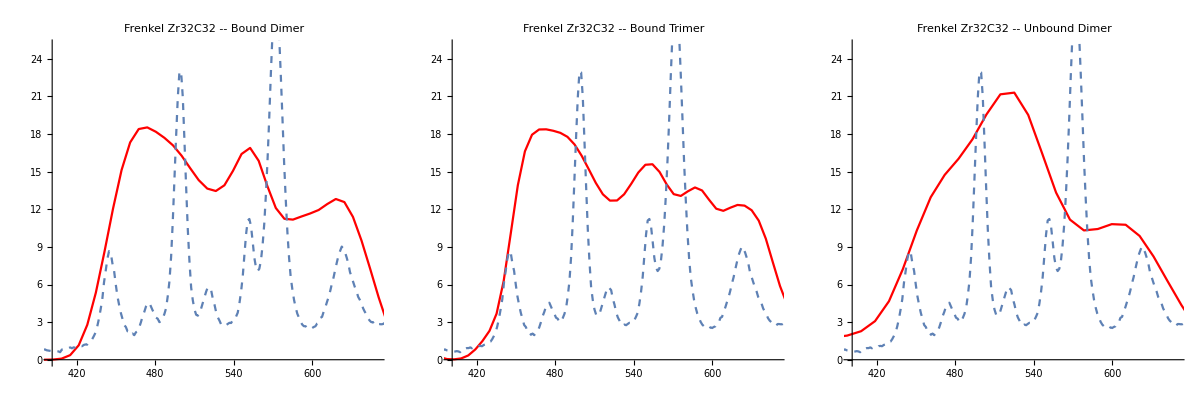

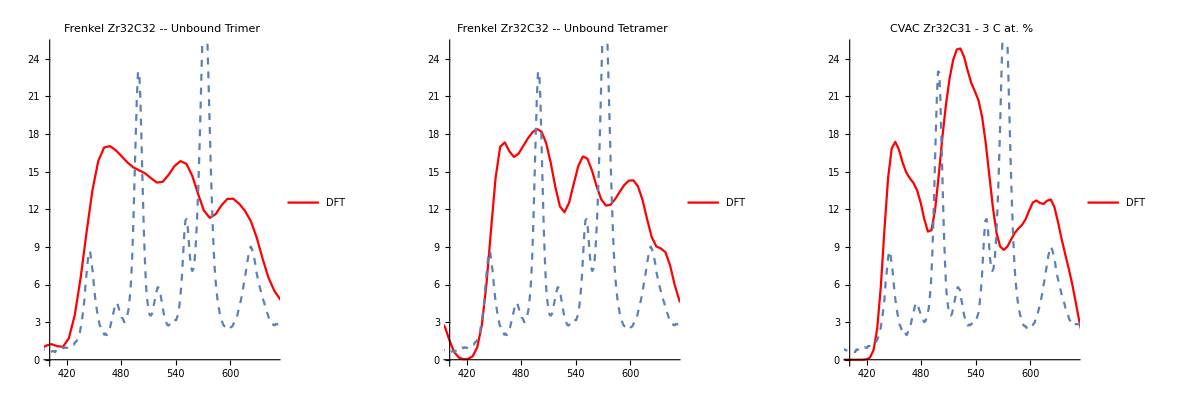

```mathematica
Carbon states
GraphicsGrid[{Table[With[{defect=i,vol=5},Show[{ListLinePlot[data2D[[defect]][[vol]],PlotRange->{{400,650},{0,25}},PlotLegends->Placed[{"DFT"},{0.7,0.7}],PlotStyle->Red,PlotLabel->names2[[defect]]],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed,PlotLegends->Placed[{"Exp"},{0.7,0.7}]]}]],{i,2,4,1}]},ImageSize->1200,Spacings->0]
GraphicsGrid[{Table[With[{defect=i,vol=5},Show[{ListLinePlot[data2D[[defect]][[vol]],PlotRange->{{400,650},{0,25}},PlotLegends->Placed[{"DFT"},{0.7,0.7}],PlotStyle->Red,PlotLabel->names2[[defect]]],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed]}]],{i,5,7,1}]},ImageSize->1200,Spacings->0]
```